```mathematica
beta=3.0
xi=1.0
phi0=0.64
```

3.

1.

0.64

```mathematica
f[phi_, per_]:=(phi/(1-phi))*((1/phi)+(((beta * per * phi0)/phi0)*(1-(phi/phi0))^-1)+(3*xi*phi^2)-phi+(((beta * per * phi0)/phi0)*(1-phi0)*(1-(phi/phi0))^-2)-3+(beta * per * phi0))-1+(2*phi)+(xi*phi^2)-(((beta * per * phi0)/phi0)*(2*phi*((1-(phi/phi0))^-1)+((phi^2)/phi0)*(1-(phi/phi0))^-2))
Solve[f[0.4, per]==0, per]
```

{{per→-1.80144×10^14}}

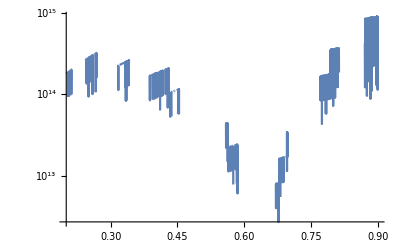

```mathematica
{{per->-1.8014398509481978*^14}}
LogPlot[per /. Solve[f[phi, per]==0, per], {phi, 0.2, 0.9}]
```

```mathematica
LogPlot[per /. Solve[f[phi, per]==0, per], {phi, 0.2,0.9}, PlotRange->{{0.2,0.9},{10^-3,10^-1}}]
```

-Graphics-

```mathematica
ContourPlot[f[phi,per]==0,{phi,0.2,0.9},{per,10^-3,10^-1}]
```

-Graphics-

```mathematica
(* I re-solved for the binodal relation (only in 3D). I'm going to put it in here and solve *)
binRel[phi_, per_]:=(phi/(1-phi))*((1/phi)+(3*per*(1-(phi/phi0))^-1)+(3*phi^2)-(phi)+(3*per*(1-phi0)*(1-(phi/phi0))^-2)-3*(1-(phi0*per)))-(1)+(2*phi)+(3*phi^2)-(3*per*(1-(phi/phi0))^-1)-((3*phi*per/phi0)*(1-(phi/phi0))^-2)
```

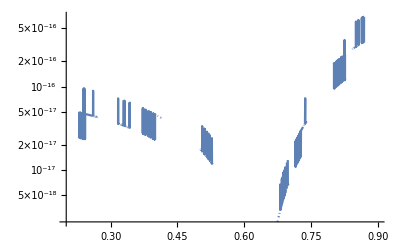

```mathematica
LogPlot[per /. Solve[binRel[phi, per]==0, per], {phi, 0.2, 0.9}]
```